### Controller Design

```mathematica
Clear["Global`*"];
```

```mathematica
Controller=Kp + Ki/s; Plant=A/(1+τ s);
```

```mathematica
ClosedSystem= (Controller Plant)/(1 + Controller Plant);
%//Simplify;
```

#### Requirements

```mathematica
settlingTimeLimit = 2;peakTimeLimit=1;peakAmpLimit=0.1;
```

```mathematica
σlimit = -Log[0.02]/settlingTimeLimit
ωdlimit = π/peakTimeLimit
ζlimit = √(Log[peakAmpLimit]^2/(π^2+Log[peakAmpLimit]^2))
```

1.95601

π

0.591155

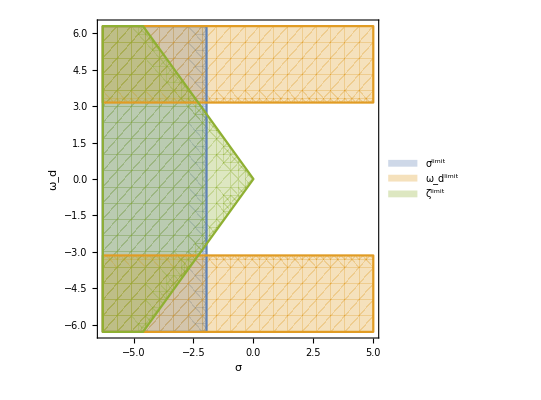

```mathematica
show1=RegionPlot[{
σ<-σlimit,
Abs[ωd]>ωdlimit,
σ^2+ωd^2≤10000&&ωd≤-Tan[ArcCos[ζlimit]]σ&&ωd>+Tan[ArcCos[ζlimit]]σ},
{σ,-ωdlimit*2,5},{ωd,-ωdlimit*2,ωdlimit*2},LabelStyle->Directive[FontSize->16],PlotLegends->{"σ^limit","ω_d^limit","ζ^limit"},Axes->True,AxesLabel->{"σ","ω_d"}]
```

#### Plant numeric values

```mathematica
A=93.8978;τ=0.3;
```

#### Place placement

```mathematica
σTrial = 5; ωdTrial = ωdlimit;
```

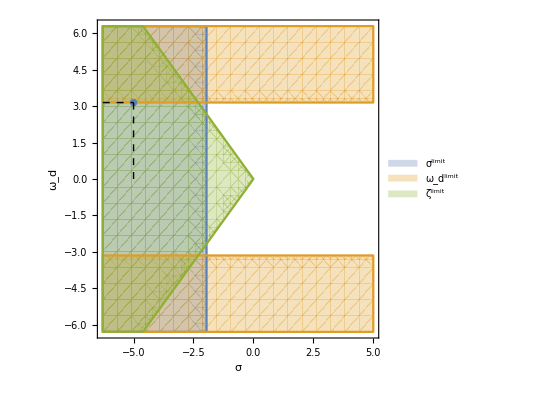

```mathematica
Show[show1,ListPlot[{{-σTrial,ωdTrial}}],Graphics[{Dashed,Line[{{-σTrial,0},{-σTrial,ωdTrial}}]}],Graphics[{Dashed,Line[{{-ωdlimit*2,ωdTrial},{-σTrial,ωdTrial}}]}]]
```

```mathematica
KpEstimate = (2 σ τ - 1)/A/.{σ->σTrial,ωd->ωdTrial}
KiEstimate = (τ(σ^2+ωd^2))/A/.{σ->σTrial,ωd->ωdTrial}
```

0.0212998

0.111407

```mathematica
ClosedSystemEvalPI = ClosedSystem/.{Kp->KpEstimate,Ki->KiEstimate}//FullSimplify;
```

```mathematica
yPI=OutputResponse[ClosedSystemEvalPITransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic,50*UnitStep[t],t];
```

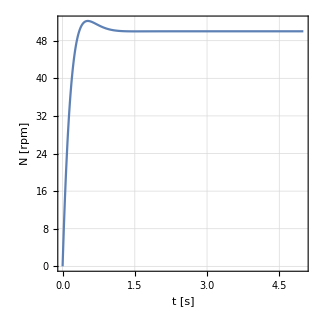

```mathematica
Plot[yPI,{t,0,5},PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"t [s]","N [rpm]"},LabelStyle->Directive[FontSize->16],PlotLegends->Automatic,AspectRatio->1]
```

```mathematica
ζ=0.2;ωn=10;kDC=1;
```

```mathematica
OutputResponse[(kDC ωn^2)/(s^2+2 ζ ωn s+ωn^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic,UnitStep[t],t];
Plot[%,{t,0,3},PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Time","Amplitude"},PlotLegends->{"k_DC/s^2 (k_DC=1,ω_n=10,ζ=0.2)"},PlotLabel->"Step Respone"];
```

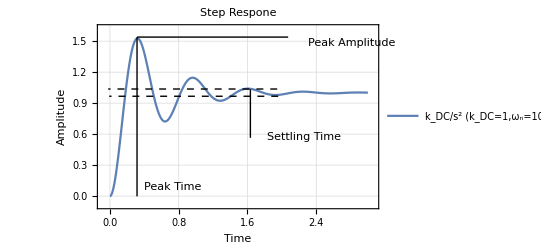

-Graphics-